```mathematica
aa[n_,x_]:=(-1/2+x)n^(1/2+x)HarmonicNumber[n,1/2+x]-(-1/2-x)n^(1/2-x)HarmonicNumber[n,1/2-x]
pl1[s_,t_]:=Plot[{Re@aa[n,s+t I],Re@aa[n,-s+t I]},{n,1,400000}]
pl1I[s_,t_]:=Plot[{Im@aa[n,s+t I],Im@aa[n,-s+t I]},{n,1,400000}]

aa1[n_,x_]:=(-1/2-x)n^(1/2-x)HarmonicNumber[n,1/2-x]
aa2[n_,x_]:=(-1/2+x)n^(1/2+x)HarmonicNumber[n,1/2+x]
pal1[s_,t_]:=Plot[{Re@aa1[n,s+t I],Re@aa2[n,s+t I]},{n,1,400000}]
pal1I[s_,t_]:=Plot[{Im@aa1[n,s+t I],Im@aa2[n,s+t I]},{n,1,400000}]
pal1t[s_,t_]:=N@Table[{Re@aa1[n,s+t I],Re@aa2[n,s+t I]},{n,1,400000,400000/30}]
pal1It[s_,t_]:=N@Table[{Im@aa1[n,s+t I],Im@aa2[n,s+t I]},{n,1,400000,400000/30}]

naa[n_,x_]:=(-1/2+x)n^(x)HarmonicNumber[n,1/2+x]-(-1/2-x)n^(-x)HarmonicNumber[n,1/2-x]
nab[n_,x_]:=(-1/2+x)n^(x)HarmonicNumber[n,1/2+x]+(-1/2-x)n^(-x)HarmonicNumber[n,1/2-x]
npl[s_,t_]:=Plot[{Re@naa[n,s+t I],Im@naa[n,s+t I]},{n,1,400000}]
nplb[s_,t_]:=Plot[{Re@nab[n,s+t I],Im@nab[n,s+t I]},{n,1,400000}]
npl1[s_,t_]:=Plot[{Re@naa[n,s+t I],Re@naa[n,-s+t I]},{n,1,400000}]
npl1I[s_,t_]:=Plot[{Im@naa[n,s+t I],Im@naa[n,-s+t I]},{n,1,400000}]
npl1b[s_,t_]:=Plot[{Re@nab[n,s+t I],Re@nab[n,-s+t I]},{n,1,400000}]
npl1Ib[s_,t_]:=Plot[{Im@nab[n,s+t I],Im@nab[n,-s+t I]},{n,1,400000}]
naa1[n_,x_]:=(-1/2-x)n^(-x)HarmonicNumber[n,1/2-x]
naa2[n_,x_]:=(-1/2+x)n^(x)HarmonicNumber[n,1/2+x]
npal1[s_,t_]:=Plot[{Re@naa1[n,s+t I],Re@naa2[n,s+t I]},{n,1,400000}]
npal1I[s_,t_]:=Plot[{Im@naa1[n,s+t I],Im@naa2[n,s+t I]},{n,1,400000}]
npal1t[s_,t_]:=N@Table[{Re@naa1[n,s+t I],Re@naa2[n,s+t I]},{n,1,400000,400000/30}]
npal1It[s_,t_]:=N@Table[{Im@naa1[n,s+t I],Im@naa2[n,s+t I]},{n,1,400000,400000/30}]
```

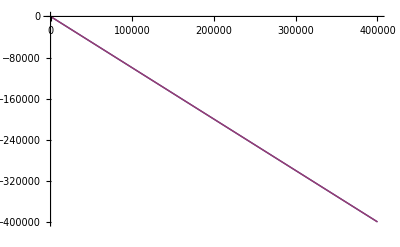

```mathematica
pal1[0,N@Im@ZetaZero@1]
```

```mathematica
N@ZetaZero@100000
```

0.5+74920.8 ⅈ

```mathematica
pal1It[0,Im@ZetaZero@2 +3]
```

{{-24.022,24.022},{-450.608,450.608},{-3095.42,3095.42},{4720.61,-4720.61},{5994.6,-5994.6},{4955.02,-4955.02},{-6616.89,6616.89},{4029.32,-4029.32},{-3830.66,3830.66},{6359.44,-6359.44},{-9475.36,9475.36},{7950.78,-7950.78},{1500.87,-1500.87},{-10760.1,10760.1},{4610.99,-4610.99},{10320.1,-10320.1},{-5679.09,5679.09},{-11727.7,11727.7},{2193.11,-2193.11},{13201.3,-13201.3},{5781.68,-5781.68},{-9352.27,9352.27},{-13747.7,13747.7},{-3249.65,3249.65},{10684.,-10684.},{14890.9,-14890.9},{6320.96,-6320.96},{-7416.76,7416.76},{-15778.1,15778.1},{-13245.2,13245.2}}

```mathematica
N@aa2[400000,.3+Im@ZetaZero@2 I+3I]
```

-1.08787×10^6-47113.5 ⅈ

```mathematica
Integrate[j^(-(1/2+x)),{j,0,n}]
```

ConditionalExpression[(2 n^(1/2-x))/(1-2 x),Re[x]<1/2]

```mathematica
FullSimplify[((2 n^(1/2-x))/(1-2 x))^-1]
```

1/2 n^(-1/2+x) (1-2 x)

```mathematica
n^(-1/2+x) (1/2- x)
```

```mathematica
(-1+A+f I)Sum[(n/j)^(A+f I),{j,1,n}]
```

(-1+A+ⅈ f) n^(A+ⅈ f) (-HurwitzZeta[A+ⅈ f,1+n]+Zeta[A+ⅈ f])

```mathematica
pr[n_,A_,f_]:=n^A Sum[j^-A (f Cos[f Log[n/j]]+(A-1) Sin[f Log[n/j]]),{j,1,n}]
pr2[n_,A_,f_]:=Sum[j^-A (f Cos[f Log[n/j]]+(A-1) Sin[f Log[n/j]]),{j,1,n}]
pr2a[n_,A_,f_]:=DiscretePlot[j^-A (f Cos[f Log[n/j]]+(A-1) Sin[f Log[n/j]]),{j,1,n}]
```

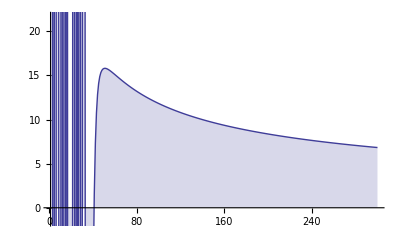

```mathematica
DiscretePlot[pr2[n,.5,N@Im@ZetaZero@100],{n,1,300}]
```

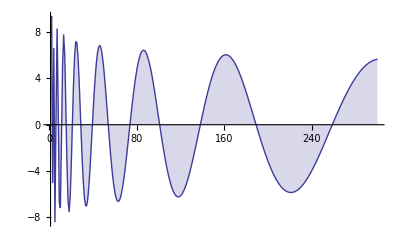

```mathematica
pr2a[300,.1, 10]
```

```mathematica
rr[n_,t_]:=Sum[j^(-1/2)(Cos[t Log[j]]+Tan[t Log[n]+ArcCot[2 t]]Sin[t Log[j]]),{j,1,n}]
rrs[n_,t_]:=Tan[t Log[n]+ArcCot[2 t]]
```

```mathematica
rr[1000,.4I+100]
```

1.76709+0.0543434 ⅈ

```mathematica
Zeta[.5-100I]
```

2.69262+0.020386 ⅈ

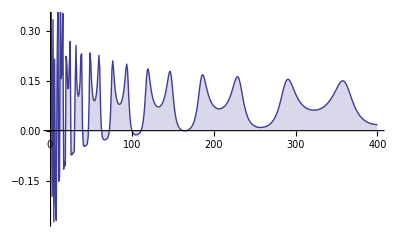

```mathematica
DiscretePlot[Re@rr[n,N@Im@ZetaZero@1+.1I],{n,1,400}]
```

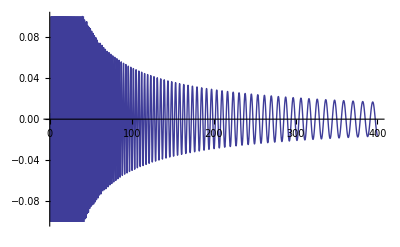

```mathematica
Plot[Re@rrs[n,100+.4I],{n,1,400}]
```

```mathematica
FullSimplify[TrigToExp[Tan[t Log[n]+ArcCot[2 t]]],Element[n,Integers]]
```

-ⅈ+(-2 ⅈ+4 t)/(-1+n^(2 ⅈ t) (1-2 ⅈ t)-2 ⅈ t)